Testing Spatial Audio on a Single Plane - 2D

## Determining Time Delays based on Ear Location [Complete]

Graphical Visualization

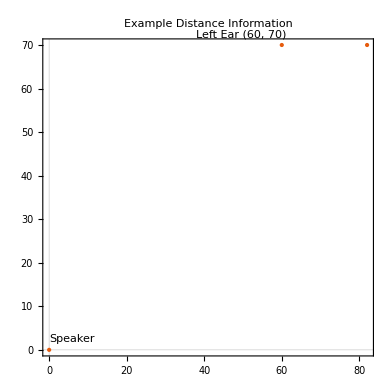

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = Quantity[√(60.^2+70.^2),"centimeters"]
distanceRightEar = Quantity[√(62.^2+70.^2), "centimeters"]
(*Angle Between Speaker and X-axis when connected as Right Triangle with Ear*)
thetaLeftEar =Quantity[ArcTan[70./60.] ,"radians"]
thetaRightEar =Quantity[ArcTan[70./62.], "radians"]
```

92.1954 cm

93.5094 cm

0.86217 rad

0.84593 rad

Speed of Sound

```mathematica
speedOfSound =StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"]
```

340.29 m/s

Determining Delays

```mathematica
delayLeftEar=distanceLeftEar/speedOfSound
delayRightEar = distanceRightEar / speedOfSound
```

0.00270932 s

0.00274793 s

## Working with Audio Functions to Channel Delay [Complete]

```mathematica
sampleAudio=Import["/Users/shubhamkumar/Downloads/prenks/Serene Queen - LDR.mp3"]
```

```mathematica
(*Doesn't Work, Stereo not split into Mono for each Channel*)
AudioChannelSeparate[sampleAudio]
```

{,}

Visualizing Audio and Trimming For Faster Processing

-Graphics-

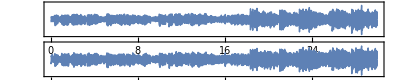

2

```mathematica
sampleAudioTrimmed = AudioTrim[sampleAudio, {10,40}]
Spectrogram[sampleAudioTrimmed]
AudioPlot[sampleAudioTrimmed]
AudioChannels[sampleAudioTrimmed]
```

Panning Test

```mathematica
leftAudio = AudioPan[sampleAudioTrimmed,-1.]
rightAudio = AudioPan[sampleAudioTrimmed, 1.]
```

```mathematica
AudioChannelCombine[{leftAudio, rightAudio}]
```

Delaying Audio For Each Channel

```mathematica
delayedLeftAudio = AudioDelay[leftAudio,delayLeftEar]
delayedRightAudio= AudioDelay[rightAudio,delayRightEar]
(*Making Sure Delay Worked*)
Duration@{delayedLeftAudio, delayedRightAudio, leftAudio, rightAudio}
```

{30.0027 s,30.0027 s,30. s,30. s}

```mathematica
spatial2dAudioTrimmed = AudioChannelCombine[{delayedRightAudio, delayedLeftAudio}]
```

Checking Differences

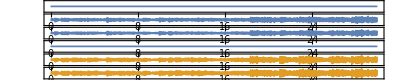

{4,2}

```mathematica
AudioPlot@{spatial2dAudioTrimmed, sampleAudioTrimmed}
AudioChannels@{spatial2dAudioTrimmed, sampleAudioTrimmed}
```

## Functional Implementation of Single Plane 2D Audio with Delay and Simple Attenuation [Complete] [Performance][ISQ Law dB Attenuation]

Combining Processes from Previous Sections + Adding in Audio Amplification

```mathematica
PlotPoint2dAudio[speakerPoint_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[{
Labeled[{speakerPointLoc[[1]], speakerPointLoc[[2]]},"Speaker"],
Labeled[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Labeled[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]
```

Implementing Inverse Square Law [Experimenting]

```mathematica
Point2dAudioV1[file_, speakerPoint_, leftEar_, rightEar_, amplificationProportion_, trimStart_, trimEnd_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, t1=trimStart, t2=trimEnd},
(*Trimming Raw Audio & Separating Audio for each Channel*)
rawAudioData = Import[fileLoc];
trimmedRawAudioData = AudioNormalize[AudioTrim[rawAudioData,{t1, t2}]];
leftAudioData = AudioPan[trimmedRawAudioData,-1.];
rightAudioData = AudioPan[trimmedRawAudioData, 1.];

(*Calculating Delays*)
leftEarDistanceFromSpeaker = Quantity[√((leftEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(leftEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
rightEarDistanceFromSpeaker = Quantity[√((rightEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(rightEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
speedOfSound = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftEarAudioDelay = leftEarDistanceFromSpeaker/speedOfSound;
rightEarAudioDelay = rightEarDistanceFromSpeaker/speedOfSound;

(*Debug*)
(*Print["Left Ear Audio Distance:"]; Print[leftEarDistanceFromSpeaker];
Print["Right Ear Audio Distance:"]; Print[rightEarDistanceFromSpeaker];
Print["Left Ear Audio Delay:"]; Print[leftEarAudioDelay];
Print["Right Ear Audio Delay:"]; Print[rightEarAudioDelay];*)

(*Audio Delaying & Trash Attenuation*)
(*leftEarAudioDelayedData = If[QuantityMagnitude[leftEarDistanceFromSpeaker] ≠ 0, 
AudioAmplify[AudioDelay[leftAudioData, leftEarAudioDelay], QuantityMagnitude[k/leftEarDistanceFromSpeaker]], 
leftAudioData];
rightEarAudioDelayedData = If[QuantityMagnitude[rightEarDistanceFromSpeaker]≠ 0, 
AudioAmplify[AudioDelay[rightAudioData, rightEarAudioDelay], QuantityMagnitude[k/rightEarDistanceFromSpeaker]], 
rightAudioData];*)

(*Audio Delaying & Less Trash Attenuation*)

(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftEarAudioDelayedData, rightEarAudioDelayedData}]]
]
```

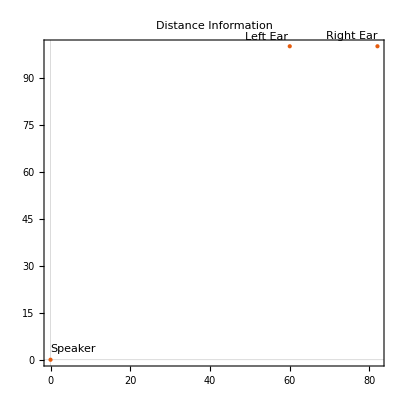

```mathematica
PlotPoint2dAudio[{0,0},{60,100},{82,100}]
```

Function Unit Tests

```mathematica
delayTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{60,100},{82,100}, 100, 0, 30]
```

Left channel is indeed louder than the right

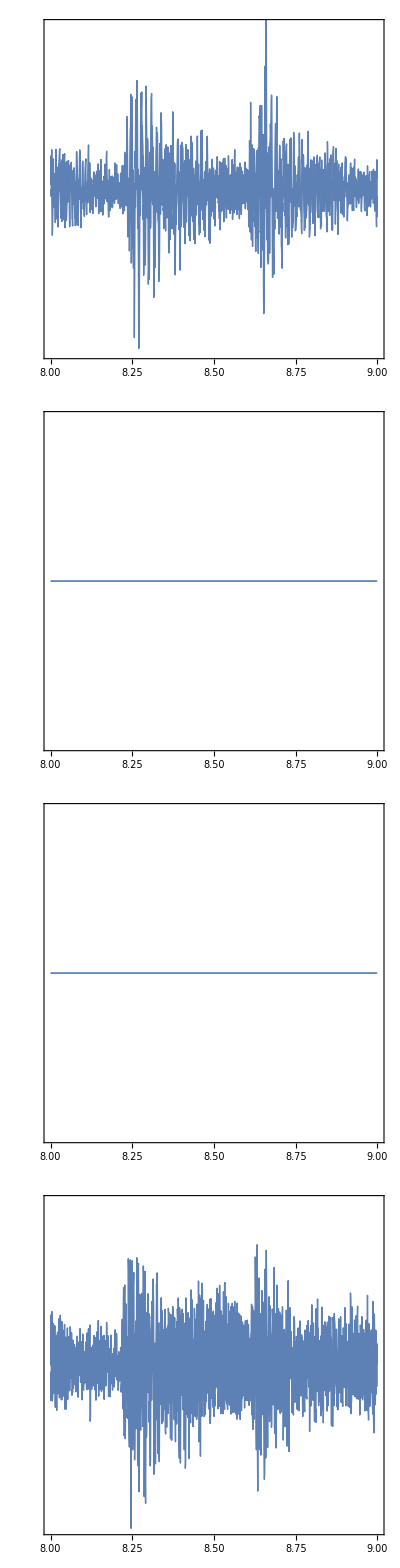

-Graphics-

4

```mathematica
AudioPlot[delayTest, PlotRange->{{8,9},{-0.8, 0.8}}]
Spectrogram[delayTest]
AudioChannels[delayTest]
```

```mathematica
delayTestLoudness =AudioLoudness[delayTest]
```

TimeSeries[…]

Speaker and Ears are all at the same location

```mathematica
(*Lmao don't run this - fixed it, its fine now*)
sanityTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{0,0},{0,0}, 100, 0, 30]
```

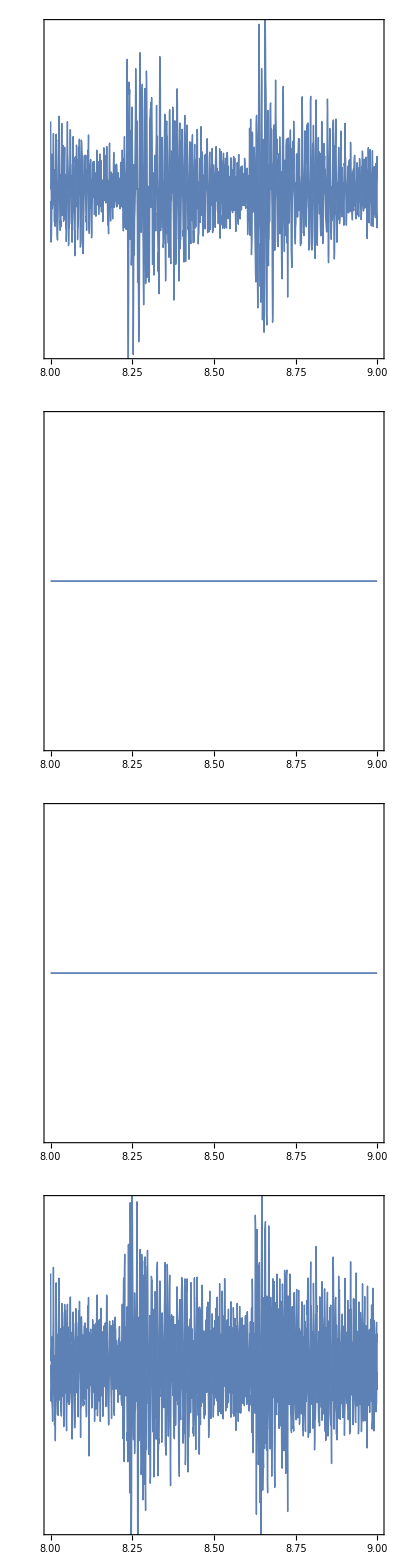

-Graphics-

4

```mathematica
AudioPlot[sanityTest, PlotRange->{{8,9},{-0.8,0.8}}]
Spectrogram[sanityTest]
AudioChannels[sanityTest]
```

```mathematica
sanityTestLoudness = AudioLoudness[sanityTest]
```

TimeSeries[…]

Comparing With Raw Audio - Can’t Quite Tell a Difference but the Audio Plot Shows that there is

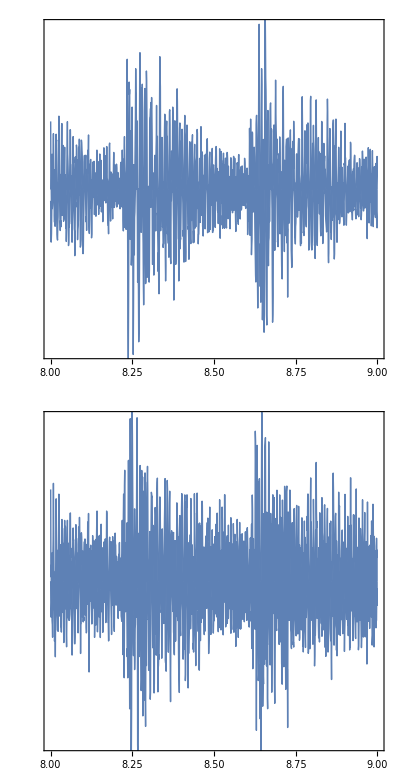

```mathematica
rawAudioComparison=AudioNormalize[AudioTrim[Import["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3"],{0,30}]]
AudioPlot[rawAudioComparison, PlotRange-> {{8,9},{-0.8, 0.8}}]
```

```mathematica
rawAudioLoudness =AudioLoudness[rawAudioComparison]
```

TimeSeries[…]

Comparing Loudness

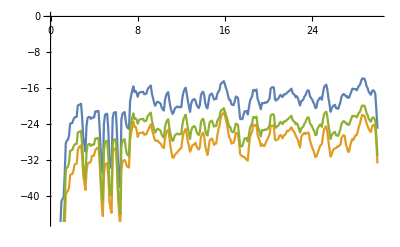

```mathematica
ListLinePlot@{rawAudioLoudness, delayTestLoudness, sanityTestLoudness}
```

## Extend Function to Understand that the Head is an Obstacle [In Progress Section: PDE TDS][Using Acoustics]

## Moving Speaker in a 2D Plane [Canceled][Performance][Using Acoustics]

Testing

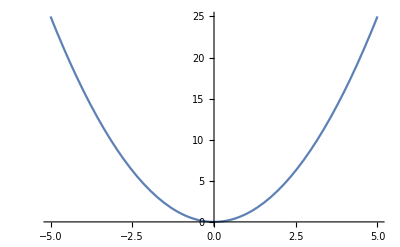

{25.,23.7656,22.5625,21.3906,20.25,19.1406,18.0625,17.0156,16.,15.0156,14.0625,13.1406,12.25,11.3906,10.5625,9.76563,9.,8.26563,7.5625,6.89063,6.25,5.64063,5.0625,4.51563,4.,3.51563,3.0625,2.64063,2.25,1.89063,1.5625,1.26563,1.,0.765625,0.5625,0.390625,0.25,0.140625,0.0625,0.015625,0.,0.015625,0.0625,0.140625,0.25,0.390625,0.5625,0.765625,1.,1.26563,1.5625,1.89063,2.25,2.64063,3.0625,3.51563,4.,4.51563,5.0625,5.64063,6.25,6.89063,7.5625,8.26563,9.,9.76563,10.5625,11.3906,12.25,13.1406,14.0625,15.0156,16.,17.0156,18.0625,19.1406,20.25,21.3906,22.5625,23.7656,25.}

81

```mathematica
Plot[x^2,{x,-5,5}]
locationVals =Table[y^2,{y,-5.,5.,0.125}]
Length[locationVals]
```

Can’t Implement this for my life

```mathematica
(*PlotPath2dAudio[speakerPath_, range_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPath, rangeLoc=range, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[Echo@Join[{
Legended[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Legended[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]},
Table[{Sin[n], Sin[2 n]}, {n, 10}]],
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]*)
```

```mathematica
(*PlotPath2dAudio[{0,0},{1,1},{2,2}, {3,3}]*)
```

Visualizing Points

```mathematica
(*points = Table[{4.n, 100.*Sin[ n]}, {n,0,8Pi, Pi/100}];
Length@points*)
```

801

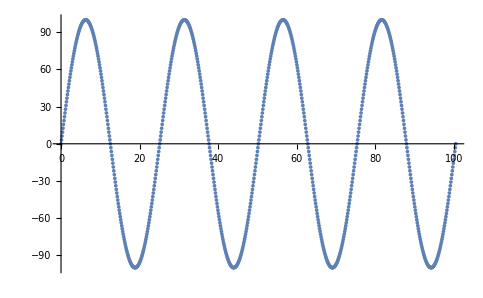

```mathematica
(*ListPlot[points, ScalingFunctions->{Identity,Identity}]*)
```

```mathematica
Path2dAudioV1[file_, speakerPath_, leftEar_, rightEar_, amplificationProportion_, duration_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPath, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, durationLoc=duration},
subtrimLengths = durationLoc/Length[speakerPath];
AudioJoin[MapIndexed[Point2dAudioV1[file, #1, leftEar, rightEar, amplificationProportion, 30+(First[#2]-1)*subtrimLengths, 30+First[#2]*subtrimLengths]&, speakerPath]]
]
```

Very Time Consuming Computation - How can I speed this up?

```mathematica
(*out = Path2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3", points, {39,-100}, {61, -100}, 100, 10]*)
```

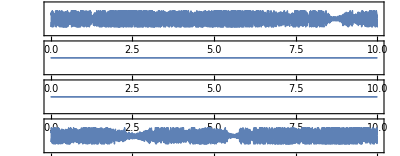

```mathematica
(*AudioPlot[out, PlotRange->{{0,10},{-2,2}}]*)
```

```mathematica
AudioNormalize[out]
```

## Doppler Effect in a 2D Plane [Canceled][Attenuation Needed][Figure out how to use Acoustics]

Source and Observer are on the Same Line, Observer is Stationary, Minimal Implementation

```mathematica
rawFrequency = Quantity[500,"Hz"]
velocitySource = Quantity[5, "m/s"]
```

500 Hz

5 m/s

```mathematica
AudioGenerator[{"Sin",100}]
```

```mathematica
sourcePath = Table[n,{n,0,25,0.25}];
Length@sourcePath;
(*Head@sourcePath
Head@{-1*#&/@sourcePath[[51;;101]]}*)
negPosi=Reverse[-1*#&/@sourcePath[[1;;50]]];
posPosi=sourcePath[[1;;51]];
sourcePath =Join[negPosi, posPosi]
Length@sourcePath
(*sourcePath = Join[sourcePath[1;;50],{-1*#&/@sourcePath[[51;;101]]}]*)
```

{-12.25,-12.,-11.75,-11.5,-11.25,-11.,-10.75,-10.5,-10.25,-10.,-9.75,-9.5,-9.25,-9.,-8.75,-8.5,-8.25,-8.,-7.75,-7.5,-7.25,-7.,-6.75,-6.5,-6.25,-6.,-5.75,-5.5,-5.25,-5.,-4.75,-4.5,-4.25,-4.,-3.75,-3.5,-3.25,-3.,-2.75,-2.5,-2.25,-2.,-1.75,-1.5,-1.25,-1.,-0.75,-0.5,-0.25,0.,0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.,10.25,10.5,10.75,11.,11.25,11.5,11.75,12.,12.25,12.5}

101

```mathematica
DopplerFormula[actualFrequency_, sourceVelocity_, observerVelocity_, soundVelocity_, observerPosition_]:=
Module[{actualFreqLoc=actualFrequency, vS=sourceVelocity, vO=observerVelocity, v=soundVelocity, poi=observerPosition},
(*Calculating Perceived Frequency*)
{If[observerPosition ≠ 0, 1/observerPosition, 5], actualFreqLoc*((v+vO)/(v-(-Sign[poi]*vS)))}
]
```

```mathematica
percFreqs=DopplerFormula [rawFrequency, velocitySource, 0, StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"],#]&/@ sourcePath
```

{507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,507.456 Hz,500. Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz,492.76 Hz}

```mathematica
rawOut = AudioJoin[AudioGenerator[{"Sin", #},0.1]&/@percFreqs]
```

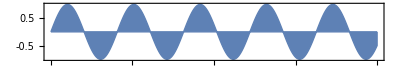

```mathematica
AudioPlot[rawOut, PlotRange->{2,2.01}]
```

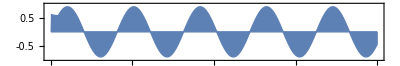

```mathematica
gaussOut = MeanFilter[rawOut,10]
AudioPlot[gaussOut, PlotRange->{2,2.01}]
```

Attenuation

## Testing PDE TIME DOMAIN Stuff *All above obsolete if this works [Working]

Tutorial Implementation

```mathematica
Ω=RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];
```

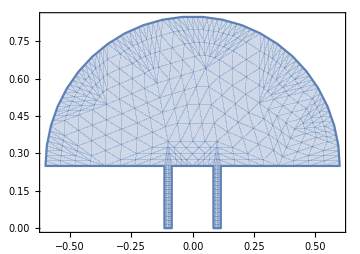

```mathematica
RegionPlot[Ω,Sequence[AspectRatio->Automatic,ImageSize->Medium], PlotPoints->10]
```

```mathematica
trbc=NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,y==0];
```

```mathematica
tabc=NeumannValue[-((I ω)/(ρ c))*p[x,y],y>1/4];
```

```mathematica
cair=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
pair=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
λ=1/10;
f=cair/λ;
```

```mathematica
pde={-((ω^2 p[x,y])/(c^2 ρ))+Inactive[Div][({{-(1/ρ),0},{0,-(1/ρ)}}.Inactive[Grad][p[x,y],{x,y}]),{x,y}]==tabc+trbc}/.{c->cair,ρ->pair,ω->2 π f};
```

```mathematica
pde
```

{-3277.37 p[x,y]+({{-0.830168,0},{0,-0.830168}}.p[x,y]{x,y}Inactive){x,y}Inactive==NeumannValue[(0.+521.61 ⅈ)-(0.+52.161 ⅈ) p[x,y],y==0]+NeumannValue[(0.-52.161 ⅈ) p[x,y],y>1/4]}

```mathematica
pfun=NDSolveValue[pde,p,{x,y}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->1/40000}}}];
```

```mathematica
pfun[0,0.6]
```

1.4629-0.665524 ⅈ

```mathematica
ContourPlot[Re[pfun[x,y]*Exp[I ω 0.001]/.{ω->2 π f}],{x,y}∈Ω,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"LightTemperatureMap",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,Frame->False,Axes->False,ImageSize->Medium]]
```

-Graphics-

Random Testing Irrelevant

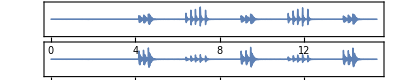

```mathematica
AudioPlot[Import["/Users/shubhamkumar/Desktop/orens.ogg"]]
```

Extending Tutorial to New Bound Conditions and Regions

```mathematica
Clear["Global`*"]
```

```mathematica
(*OΩ=RegionDifference[RegionUnion[Rectangle[{0,0},{0.25,0.25}],Rectangle[{0.25,0.05},{0.4,0.0625}],Disk[{0,0.25},0.125,{0,2Pi}]],Disk[{0,0.25},0.025]];*)
OΩ = RegionDifference[RegionDifference[Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1}, 0.025]],Disk[{0.25,0},0.0125]];
(*RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];*)
(*p=RegionUnion[Disk[{0,1/4},3/5,{0,π}],Rectangle[{-(23/200),0},{-(17/200),1/4}],Rectangle[{17/200,0},{23/200,1/4}]];*)
```

```mathematica
RegionPlot[OΩ,Sequence[AspectRatio->Automatic,ImageSize->Medium], PlotStyle->"Scientific"]
```

-Graphics-

```mathematica
(*Absorbing Boundary Condition*)
(*Gabc=NeumannValue[-((I ω)/(ρ c))*p[x,y],y>0];
Grbc = NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,x>0.2];
Gabc2 = NeumannValue[-((I ω)/(ρ c))*p[x,y],0.025>x>-0.025&&0.275>y>0.225];*)
```

```mathematica
Gabc = NeumannValue[-((I ω)/(ρ c))*p[x,y],y≥0.0125&&x≤ 0.2375];
Grbc = NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,0.0125>y≥0&&0.25≥x> 0.2375];
```

```mathematica
(*IDK how to do booleans clearly*)
0<1<=1&&2<=2
```

True

```mathematica
(*Subscript[Γ,RBC]=NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,y==0];*)
```

```mathematica
(*Params*)
Cair=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Pair=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
(*Sound Attributes*)
Oλ=1/10;
Of=Cair/Oλ;
```

```mathematica
Opde={-((ω^2 p[x,y])/(c^2 ρ))+Inactive[Div][({{-(1/ρ),0},{0,-(1/ρ)}}.Inactive[Grad][p[x,y],{x,y}]),{x,y}]==Gabc+Grbc}/.{c->Cair,ρ->Pair,ω->2 π Of}
```

{-3277.37 p[x,y]+({{-0.830168,0},{0,-0.830168}}.p[x,y]{x,y}Inactive){x,y}Inactive==NeumannValue[(0.+521.61 ⅈ)-(0.+52.161 ⅈ) p[x,y],0.0125>y≥0&&0.25≥x>0.2375]+NeumannValue[(0.-52.161 ⅈ) p[x,y],y≥0.0125&&x≤0.2375]}

```mathematica
OΩ
```

BooleanRegion[#1&&!#2&&!#3&,{Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1},0.025],Disk[{0.25,0},0.0125]}]

```mathematica
pfun=NDSolveValue[Opde,p,{x,y}∈OΩ,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->1/40000}}}];
```

```mathematica
pfun
```

InterpolatingFunction[…]

Visual 2D

```mathematica
ContourPlot[Re[pfun[x,y]*Exp[I ω 0]/.{ω->2 π Of}],{x,y}∈OΩ,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"SunsetColors",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,Axes->False,ImageSize->Medium, PlotLegends->Automatic]]
```

-Graphics-

Animated Visual 2D

```mathematica
frames=Table[ContourPlot[Re[pfun[x,y]*Exp[I ω t]/.{ω->2 π Of}],{x,y}∈OΩ,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"SunsetColors",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,PlotLegends->Automatic]],{t,0,0.001,0.001/50}];ListAnimate[frames]
```

Visual 3D

```mathematica
Abs[pfun[0,0]]
```

1.55952

```mathematica
Plot3D[Re[pfun[x,y]], {x,0,0.25}, {y,0,0.25}, PlotStyle->"Scientific", PlotRange->{{0,0.25},{0,0.25},{-5,5}}]
(*Plot3D[Im[pfun[x,y]], {x,0,0.25}, {y,0,0.25}]
Plot3D[Abs[pfun[x,y]], {x,0,0.25}, {y,0,0.25}]*)
```

-Graphics3D-

Animated Visual 3D

```mathematica
frames3d = Animate[Plot3D[Re[pfun[x,y]*Exp[I ω 0.001t]/.{ω->2 π Of}], {x,0,0.25}, {y,0,0.25},PlotRange->{{0,0.25},{0,0.25},{-5,5}},PerformanceGoal->"Quality",ViewPoint->{Pi,2Pi*t,2}],{t,0,1}]
```

```mathematica
Export["/Users/shubhamkumar/Desktop/oren3.gif",frames3d]
```

/Users/shubhamkumar/Desktop/oren3.gif

#### Capturing Sound Pressure Data at each Ear // I was first experimenting with movement hence the 3 parameters in map. Got ahead of myself : (

```mathematica
Re[pfun[0,0.20]*Exp[I ω t]/.{ω->2 π Of}]
```

Re[(-1.00565+1.12276 ⅈ) ⅇ^((0.+21572.9 ⅈ) t)]

```mathematica
(*Table[{x,x},{x, 0,0.1,0.1/1000}][[1;;10]]*)
```

```mathematica
(*ListPlot[{ Table[{x,√(0.05^2-(x-0.05)^2)},{x, 0,0.1,0.1/1000}]}, PlotRange->{{0, 0.1}, {0,0.1}},AspectRatio->1]*)
```

```mathematica
(*PressureOutList = Re[pfun[#[[1]],#[[2]]]*Exp[I ω #[[3]]]/.{ω->2 π Of}]&/@Transpose[{Table[x,{x, 0,0.1,0.1/10000}], Table[√(0.05^2-(y-0.05)^2),{y, 0,0.1,0.1/10000}], Table[t, {t,0,0.01,0.01/10000}]}];
ListPlot@PressureOutList
(*Re[pfun[0.1,0.1]*Exp[I ω #]/.{ω->2 π Of}]&/@Table[n, {n,0,10,0.1}]*)*)
```

Generating List of Points for Left and Right Ear

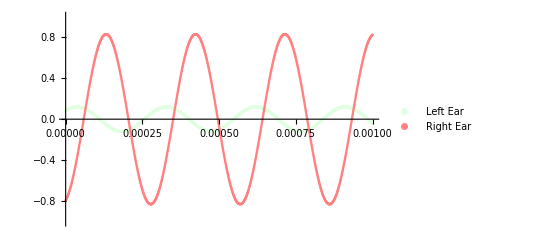

```mathematica
LeftEar ={#, Re[pfun[0.075,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/1000}];
RightEar ={ #,Re[pfun[0.125,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/1000}];
l1 = ListPlot[LeftEar,PlotLegends->{"Left Ear"},PlotStyle->{LightGreen}, PlotRange->{{0,0.001}, {-1,1}}];
l2 = ListPlot[RightEar,PlotLegends->{"Right Ear"},PlotStyle->{Pink},PlotRange->{{0,0.001}, {-1,1}}];
Show[l1,l2]
```

Finding Minima and Maxima Data

```mathematica
Max[#[[2]]&/@LeftEar]
Min[#[[2]]&/@LeftEar]
Max[#[[2]]&/@RightEar]
Min[#[[2]]&/@RightEar]
```

0.120121

-0.120121

0.827438

-0.827436

Setting Initial Conditions

```mathematica
Manipulate[Show[ListPlot[LeftEar],Plot[0.12012126831185457 Sin[b x +c],{x,0,0.001}]], {b,0,100000},{c,0,5}]
bEstL = 21400;
cEstL = 0.88;
```

```mathematica
Manipulate[Show[ListPlot[RightEar],Plot[0.8274376082610522 Sin[b x +c],{x,0,0.001}]], {b,0,100000},{c,0,5}]
bEstR=21600;
cEstR = 4.95;
```

Fitting the Model

Left Ear

```mathematica
fmL =NonlinearModelFit[LeftEar,0.12012126831185457 Sin[b x+c],{{b,21400}, {c,0.88}},x, MaxIterations->Automatic, Method->NMinimize];
```

```mathematica
LeftEarFit ={ #,fmL[#]}&/@Table[t, {t,0,0.001,0.001/1000}];
```

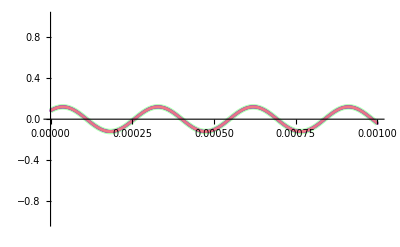

```mathematica
fitL = ListPlot[LeftEarFit,PlotStyle->{Blue, Opacity[0.3]}, PlotRange->{{0,0.001}, {-1,1}}];
rawL = ListPlot[LeftEar, PlotStyle->{Pink, Opacity[0.3]}, PlotRange->{{0,0.001}, {-1,1}}];
funcL=Plot[fmL[x],{x,0,0.0010},PlotRange->{{0,0.001}, {-1,1}}, PlotStyle->{Green, Opacity[0.3],Thickness[0.01]}];
Show[funcL,fitL,rawL]
```

```mathematica
Normal[fmL]
```

0.120121 Sin[0.762724+21572.9 x]

Right Ear

```mathematica
fmR =NonlinearModelFit[RightEar,0.8274376082610522 Sin[b x+c],{{b,21600}, {c,4.95}},x, MaxIterations->Automatic, Method->NMinimize];
```

```mathematica
fmRManual[x_]:=0.8274376082610522 Sin[21600x+4.95]
```

```mathematica
(*RightEarFitManual ={ #,fmRManual[#]}&/@Table[t, {t,0,0.001,0.001/1000}]*)
RightEarFit ={ #,fmR[#]}&/@Table[t, {t,0,0.001,0.001/1000}];
(*fitRManual = ListPlot[RightEarFitManual,PlotStyle->{Blue, Opacity[0.3]}, PlotRange->{{0,0.001}, {-1,1}}];*)
```

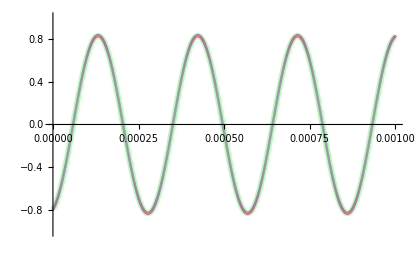

```mathematica
fitR = ListPlot[RightEarFit, PlotStyle->{Blue, Opacity[0.3]}, PlotRange->{{0,0.001}, {-1,1}}];
rawR = ListPlot[RightEar, PlotStyle->{Pink, Opacity[0.3]}, PlotRange->{{0,0.001}, {-1,1}}];
funcR =Plot[fmR[x],{x,0,0.0010},PlotRange->{{0,0.001}, {-1,1}}, PlotStyle->{Green, Opacity[0.3],Thickness[0.01]}];
Show[funcR,fitR,rawR]
```

```mathematica
Normal[fmR]
```

0.827438 Sin[5.01114+21572.9 x]

Fourier to Decompose the Graph

Making The NLMFs Audible

```mathematica
leftEarAudioFreqPhase = AudioGenerator[{"Sin",21572.932190413565 /10,0.7627240470048269/10}];
rightEarAudioFreqPhase = AudioGenerator[{"Sin",21572.932516494737/10,5.0111372046811535/10}];
```

```mathematica
leftEarAudioMono = AudioPan[leftEarAudioFreqPhase, -1.]
rightEarAudioMono =AudioPan[rightEarAudioFreqPhase, 1.]
```

```mathematica
leftEarAudio = AudioAmplify[leftEarAudioMono,0.12012126831185457 ]
rightEarAudio = AudioAmplify[rightEarAudioMono,0.8274376082610522]
```

```mathematica
finalAudio =AudioChannelCombine[{leftEarAudio, rightEarAudio}]
```

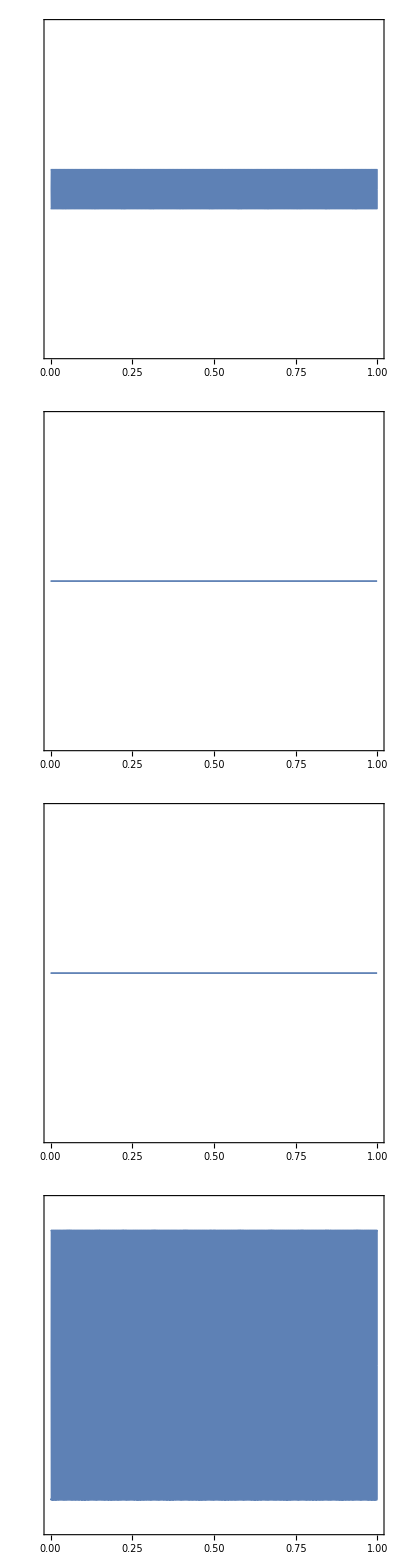

```mathematica
AudioPlot[finalAudio]
```

```mathematica
Spectrogram[finalAudio]
```

-Graphics-

Again for Right Ear

```mathematica
(*0.0022092735452950746Sin[0.998016746385263x+2.6597424066568682]*)
```

## Go again for PDE FREQUENCY DOMAIN : ( [Not Started][IFT?]

## Functional Implementation of Single Plane 2D with Acoustics [Not Started]